# Saha equation

## Solving the Saha equation for the fraction of free electrons, Xe

### As a function of temperature

Define parameters

```mathematica
Clear["Global'*"]
(*Clear[mp,me,mH,B,eta,Z,T];*)
mp=9.3828*10^8;(*ev/c^2, 1.67*10^-27 kg*)
me=0.511*10^6; (*ev/c^2, 9.11*10^−31 kg*)
mH=mp+me-13.6; (*ev/c^2, 1.6735575*10^-27 kg*)
B=mp+me-mH;
eta=6*10^-10;
Z=N[Zeta[3]];
(*Z=1.20206;*)
```

Saha equation

```mathematica
equation=(1-Xe)/Xe^2==2*Z/Pi^2*eta*(2*Pi*T/me)^(3/2)Exp[B/T];
(*T=0.3;*)
NSolve[equation,Xe]
```

{{Xe→(0.5 2.71828^(-13.6/T) (-1.58692×10^17-1. √(2.51831×10^34+6.34768×10^17 2.71828^(13.6/T) T^(3/2))))/T^(3/2)},{Xe→(0.5 2.71828^(-13.6/T) (-1.58692×10^17+√(2.51831×10^34+6.34768×10^17 2.71828^(13.6/T) T^(3/2))))/T^(3/2)}}

Define a range of values for T

```mathematica
TValues = Range[0,1];
```

Solve the equation for Xe for each value of T

```mathematica
XeValues = Xe /.NSolve[equation, Xe][[2]];
```

Plot Xe vs T

General::munfl: 1/2.71828^665734. is too small to represent as a normalized machine number; precision may be lost.

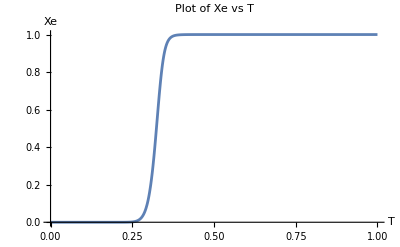

```mathematica
Plot[XeValues, {T, Min[TValues], Max[TValues]}, 
  AxesLabel -> {"T", "Xe"}, 
  PlotLabel -> "Plot of Xe vs T"]
```

```mathematica
eq[T_] := (1 - Xe)/Xe^2 == (2*Z/Pi^2)*eta*(2*Pi*T/me)^(3/2)*Exp[B/T]
result = FindRoot[eq[T] /. Xe -> 0.1, {T, 0.3}];
T_rec = T /. result
```

0.296095

### As a function of redshift

Define parameters

```mathematica
Clear["Global'*"]
(*Clear[mp,me,mH,B,eta,Z,z,T0];*)
mp=9.3828*10^8;(*ev/c^2, 1.67*10^-27 kg*)
me=0.511*10^6; (*ev/c^2, 9.11*10^−31 kg*)
mH=mp+me-13.6; (*ev/c^2, 1.6735575*10^-27 kg*)
B=mp+me-mH;
eta=6*10^-10;
ζ[3];
Z=1.20205;
kB=8.617333262*10^-5; (*eV/K*)
T0=2.725*kB;
```

Saha equation

```mathematica
equation=(1-Xe)/Xe^2==2*Z/Pi^2*eta*(2*Pi*T0*(1+z)/me)^(3/2)Exp[B/T0/(1+z)];
NSolve[equation,Xe]
```

{{Xe→(0.5 2.71828^(-57916.1/(1.+z)) (-4.4101×10^22-1. √(1.9449×10^45+1.76404×10^23 2.71828^(57916.1/(1.+z)) (1.+z)^(3/2))))/(1.+z)^(3/2)},{Xe→(0.5 2.71828^(-57916.1/(1.+z)) (-4.4101×10^22+√(1.9449×10^45+1.76404×10^23 2.71828^(57916.1/(1.+z)) (1.+z)^(3/2))))/(1.+z)^(3/2)}}

Define a range of values for z

```mathematica
zValues = Range[0.01,3000];
```

Solve the equation for Xe for each value of z

```mathematica
XeValues = Xe /.NSolve[equation, Xe][[2]];
```

Plot Xe vs z

General::munfl: 1/2.71828^54063.3 is too small to represent as a normalized machine number; precision may be lost.

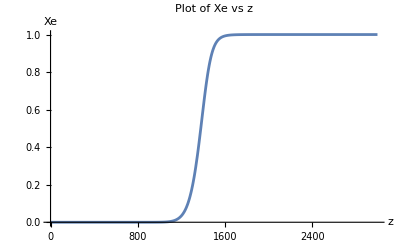

```mathematica
Plot[XeValues, {z, Min[zValues], Max[zValues]}, 
  AxesLabel -> {"z", "Xe"}, 
  PlotLabel -> "Plot of Xe vs z"]
```

```mathematica
eq[z_] := (1-Xe)/Xe^2==2*Z/Pi^2*eta*(2*Pi*T0*(1+z)/me)^(3/2)Exp[B/T0/(1+z)]
result = FindRoot[eq[z] /. Xe -> 0.1, {z, 1320}]
z_rec = z /. result
```

{z→1259.93}

1259.93